```mathematica
Clear[e0,mat,k,V0]
e0[n_,k_]=(k+2π*n)^2/2
mat[V0_,k_,enk_]={{e0[-2,k]-enk,V0/2,0,0,0},{V0/2,e0[-1,k]-enk,V0/2,0,0},{0,V0/2,e0[0,k]-enk,V0/2,0},{0,0,V0/2,e0[1,k]-enk,V0/2},{0,0,0,V0/2,e0[2,k]-enk}};
(*mat={{e0[-1,k]-enk,V0/2,0},{V0/2,e0[0,k]-enk,V0/2},{0,V0/2,e0[1,k]-enk}};*)
```

1/2 (k+2 n π)^2

```mathematica
NullSpace[mm/.{enk->sol[[3]]}/.{k->ks[[3]]}]
```

{{0.000271781,-0.0147982,-0.0474685,-0.998628,0.0164341}}

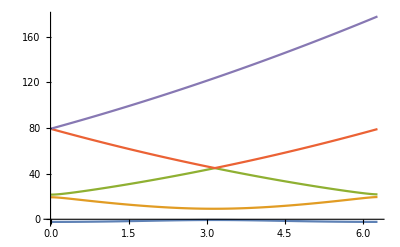

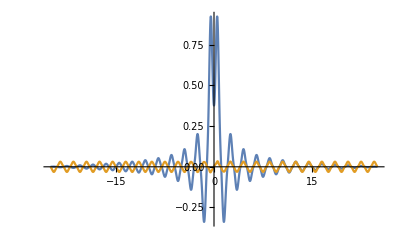

```mathematica
mm=mat[10,k,enk];
sol=enk/.NSolve[Det[mm]==0,enk];
Plot[Evaluate[Re[sol]],{k,0,2π},PlotRange->Full,PlotPoints->200,MaxRecursion->5]
length=50;
ks=Table[kk,{kk,0,2π,2π/length}];
fs=Table[NullSpace[mm/.{enk->sol[[1]]}/.{k->ks[[ii]]}],{ii,length}];
psis=Table[(ⅇ^(ⅈ*k*r)fs[[ii]].ⅇ^(2π ⅈ ( Range[Length[mm]]-Length[mm]+2)*r))[[1]]/.{k->ks[[ii]]},{ii,length}];
psis=Table[pp*(pp/.{r->0})*/Abs[pp/.{r->0}],{pp,psis}];
Plot[{Re[Mean[psis]/.{r->x}],Im[Mean[psis]/.{r->x}]},{x,-length/2,length/2},PlotRange->Full]
```